# Data preprocessing: Saiz et al 2016 data set NANOG, GATA6

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

## Unify notations

```mathematica
fileNamesRaw=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
RenameFile[#,StringReplace[#,".mx"->"SaizNotation.mx"]]&/@fileNamesRaw;
```

```mathematica
fNamesSaiz=FileNames["*FinalDataSaizNotation.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeaturesSaiz=("NucleiFeatures"/.Import[#])&/@fNamesSaiz;
```

```mathematica
appendRules[nucleusFeatures_]:=Join[nucleusFeatures,{"TE/ICM"->If[("Identity.km"/.#)≠"TE","ICM","TE"],"Quadrant"->Switch[("Identity.km"/.#),"TE","TE","DP","N+G6+","DN","N-G6-","EPI","N+G6-","PRE","N-G6+"],"Nanog-AvgShifted"->Exp["Nanog-ebLogCor"/.#],"Gata6-AvgShifted"->Exp["Gata6-ebLogCor"/.#]}&@nucleusFeatures]
```

```mathematica
Table[nucleiFeaturesSaiz=("NucleiFeatures"/.Import[#])&@fNamesSaiz[[i]];nucleiFeatures=appendRules/@nucleiFeaturesSaiz;stagingSaiz=("Staging"/.Import[#])&@fNamesSaiz[[i]];
staging={stagingSaiz[[2]],stagingSaiz[[4]],Switch[stagingSaiz[[3]],"3.5ncb",3.5,"4.0ncb",4.0,"4.5ncb",4.5]};
globalFeatures=("GlobalFeatures"/.Import[#])&@fNamesSaiz[[i]];
fNameExport=StringReplace[fNamesSaiz[[i]],"SaizNotation.mx"->".mx"];
exportData={"NucleiFeatures"->nucleiFeatures,"GlobalFeatures"->globalFeatures,"Staging"->staging};Export[fNameExport,exportData],{i,1,Length[fNamesSaiz]}]
```

## Extra category for less than 32 cells

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
pos=Position[Length/@nucleiFeatures,z_/;z<32]
```

{{43},{44},{45},{46},{47},{60},{79},{121},{122},{124}}

```mathematica
(data=Import[finalFNames[[#[[1]]]]];Print[Length["NucleiFeatures"/.data]];newStage=("Staging"/.data)/.(3.5->3.0);dataNewStage=data/.Rule["Staging",_]->Rule["Staging",newStage];
dataNew=dataNewStage/.Rule["CellNumberStage",_]->Rule["CellNumberStage",3.0];
Print["Staging"/.dataNew];
Print["GlobalFeatures"/.dataNew];
Print[("NucleiFeatures"/.data)==("NucleiFeatures"/.dataNew)];
Export[finalFNames[[#[[1]]]],dataNew])&/@pos
```

15

{<32,060314_1_1,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

16

{<32,060314_1_2,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

14

{<32,060314_1_3,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

20

{<32,060314_1_4,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

16

{<32,060314_1_5,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

29

{<32,060414_1_9,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

29

{<32,061014_1_4,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

31

{32_64,072814_R3F_LM1,3.}

{Stage→32_64,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

31

{32_64,072814_R3F_LM2,3.}

{Stage→32_64,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

31

{<32,072814_R3P_LM2,3.}

{Stage→<32,ProximityCellGraph→-Graphics3D-,DelaunayCellGraph→-Graphics3D-}

True

## Plot preprocessed data

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
nucleiFeaturesICM=Table[Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&],{i,1,Length[nucleiFeatures]}];
```

```mathematica
exprICM={"Nanog-AvgShifted","Gata6-AvgShifted"}/.nucleiFeaturesICM;
```

```mathematica
exprICMByStage=Table[Select[Transpose[{staging,exprICM}],#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
Length/@exprICMByStage
```

{54,34,49}

```mathematica
Length[Flatten[#[[All,2]],1]]&/@exprICMByStage
```

{1057,918,1994}

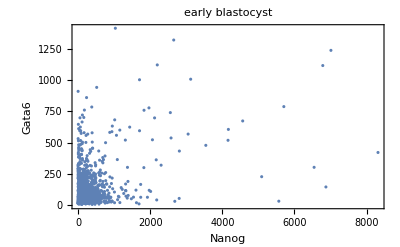
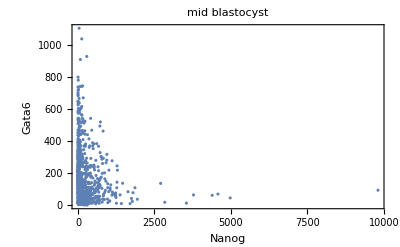
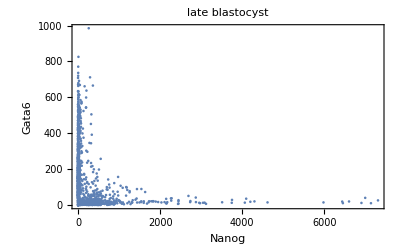
{-Graphics-,-Graphics-,-Graphics-}ICM cells

```mathematica
Labeled[Table[Show[ListPlot[#[[1;;2]]&/@Flatten[exprICMByStage[[i,All,2]],1],PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Nanog","Gata6"}],ImageSize->400,PlotLabel->({"early","mid","late"}[[i]]<>" blastocyst")],{i,1,3}],"ICM cells", Top]
```

## Plot populations

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.Import[#])&/@finalFNames;
```

```mathematica
staging=("Staging"/.Import[#])&/@finalFNames;
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
popCountICM=Table[{populationsICM[[i,1]],{#,Count[populationsICM[[i,2,All,2]],#]}&/@{"N+G6+","N-G6-","N+G6-","N-G6+"}},{i,1, Length[populationsICM]}];
```

```mathematica
popCountICMByStage=Table[Select[popCountICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
populationsByStageICM=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
popCountByStageICM=Table[{#,Count[Flatten[populationsByStageICM[[i,All,2]],1][[All,2]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,35},{N+G6+,779},{N+G6-,112},{N-G6+,131}},{{N-G6-,20},{N+G6+,429},{N+G6-,138},{N-G6+,331}},{{N-G6-,252},{N+G6+,200},{N+G6-,524},{N-G6+,1018}}}

```mathematica
popCountByStageICMTotal=Table[{#,Count[Flatten[populationsByStageICM[[i]][[All,2]]],#]}&/@{"N-G6-","N+G6+","N+G6-","N-G6+"},{i,1,3}]
```

{{{N-G6-,35},{N+G6+,779},{N+G6-,112},{N-G6+,131}},{{N-G6-,20},{N+G6+,429},{N+G6-,138},{N-G6+,331}},{{N-G6-,252},{N+G6+,200},{N+G6-,524},{N-G6+,1018}}}

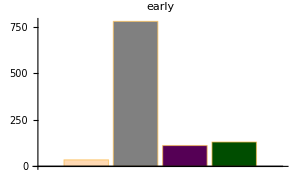
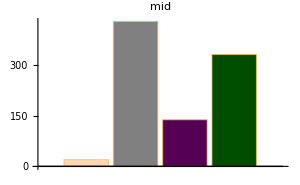
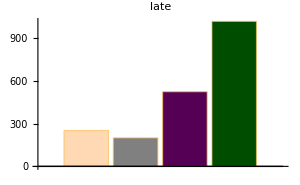

```mathematica
Labeled[Row[Table[BarChart[popCountByStageICMTotal[[i,All,2]],ImageSize->300,PlotLabel->Style[#,20,Black]&@({"early","mid","late"}[[i]]),ChartStyle->populationsColours,AxesStyle->Directive[Black,20]],{i,1,3}],"   "],SwatchLegend[populationsColours,{"DN","DP","Epi","PrE"}],Right]
```

#### Export absolute number of cells for each population to generate bar plot

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\populationCountByStage.xlsx"}],{"early"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[1]]],
"mid"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[2]]],
"late"->Join[{{"Count for different populations", "","",DateString[]},{"ICM cells, Staging by cell number, Expression levels z-corected and aligned","each row represents one embryo"},{"N+G6+","N-G6-","N+G6-","N-G6+"}},#[[-1,All,2]]&/@popCountICMByStage[[3]]]}]
```

## ICM cells positive and negative

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
popValues={"TE/ICM","Quadrant"}/.nucleiFeatures;
```

```mathematica
popValuesICM=Table[Select[popValues[[i]],#[[1]]≠"TE"&],{i,1,Length[popValues]}];
```

```mathematica
populationsICM=Transpose[{staging,popValuesICM}];
```

```mathematica
populationsICMByStage=Table[Select[populationsICM,#[[1,3]]==i&],{i,{3.5,4.0,4.5}}];
```

#### Nanog

```mathematica
nanogPositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{28,15,23,31,10,14,19,19,13,29,26,27,14,14,15,11,8,9,7,8,11,12,19,11,15,17,10,9,13,13,26,24,21,30,19,14,15,28,9,14,22,21,9,4,18,20,12,16,11,21,5,18,21,23},{23,24,23,20,12,15,10,15,26,19,16,8,10,15,25,11,11,28,25,18,14,11,18,13,9,9,25,11,16,8,18,28,24,9},{16,20,22,19,30,19,10,15,15,22,25,25,22,17,13,24,27,15,18,21,9,19,8,13,13,18,14,23,14,15,16,18,14,0,9,4,0,2,5,10,10,14,12,23,1,14,10,9,12}}

```mathematica
Length/@nanogPositiveByStage
```

{54,34,49}

```mathematica
nanogNegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"N-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{1,6,4,1,0,2,0,0,1,0,1,2,4,1,4,6,9,1,8,5,3,1,3,5,0,0,2,5,0,6,4,3,0,1,11,0,0,1,0,1,6,1,3,8,6,10,3,4,8,2,8,2,2,1},{5,1,5,12,8,13,16,13,1,9,4,12,12,10,8,14,13,3,4,7,10,12,9,8,19,9,4,14,24,32,10,5,2,23},{9,3,21,12,12,11,18,22,14,20,7,17,18,26,27,18,19,23,20,20,18,23,21,23,16,16,15,17,16,20,16,12,22,56,77,73,86,58,32,29,28,19,15,16,70,30,14,75,20}}

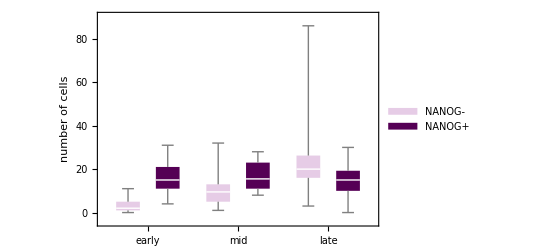

```mathematica
BoxWhiskerChart[Transpose[{nanogNegativeByStage,nanogPositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"NANOG-","NANOG+"}),ChartStyle->{Lighter[Purple,0.8],Darker[Purple]}]
```

#### Gata6

```mathematica
gata6PositiveByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6+"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{29,20,25,28,8,14,18,19,14,29,27,26,9,13,14,8,12,9,9,9,9,11,17,14,15,16,11,8,13,19,20,25,16,29,29,14,15,29,8,15,25,16,11,8,16,19,15,19,19,22,10,16,23,18},{28,25,28,29,16,21,17,15,27,26,20,11,12,23,27,18,17,31,28,25,23,22,27,19,20,11,26,15,21,25,28,30,26,23},{25,23,43,14,29,9,19,26,15,30,32,41,32,29,30,21,27,23,21,20,18,24,18,19,17,16,16,18,14,19,16,17,20,28,44,32,34,32,28,28,28,19,18,17,48,31,14,56,20}}

```mathematica
gata6NegativeByStage=Table[Count[#,{y_,z_}/;StringContainsQ[z,"G6-"]]&/@populationsICMByStage[[i,All,2]],{i,1,3}]
```

{{0,1,2,4,2,2,1,0,0,0,0,3,9,2,5,9,5,1,6,4,5,2,5,2,0,1,1,6,0,0,10,2,5,2,1,0,0,0,1,0,3,6,1,4,8,11,0,1,0,1,3,4,0,6},{0,0,0,3,4,7,9,13,0,2,0,9,10,2,6,7,7,0,1,0,1,1,0,2,8,7,3,10,19,15,0,3,0,9},{0,0,0,17,13,21,9,11,14,12,0,1,8,14,10,21,19,15,17,21,9,18,11,17,12,18,13,22,16,16,16,13,16,28,42,45,52,28,9,11,10,14,9,22,23,13,10,28,12}}

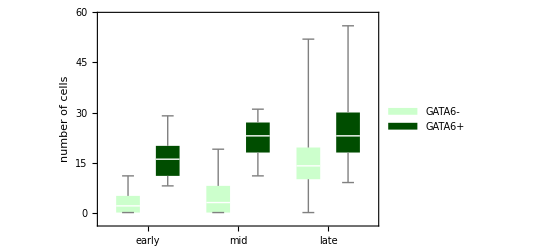

```mathematica
BoxWhiskerChart[Transpose[{gata6NegativeByStage,gata6PositiveByStage}],ChartLabels->{{"early","mid","late"},None},FrameLabel-> {None,"number of cells"},FrameStyle->Directive[Black,20],ChartLegends->(Style[#,Black,20]&/@{"GATA6-","GATA6+"}),ChartStyle->{Lighter[Green,0.8],Darker[Green,0.7]}]
```

#### Export

```mathematica
allCells=Transpose[{nanogNegativeByStage[[#]],nanogPositiveByStage[[#]],gata6NegativeByStage[[#]],gata6PositiveByStage[[#]]}]&/@{1,2,3};
```

```mathematica
exportList=Table[{"early","mid","late"}[[i]]->Join[{{"Our embryo data: number of positive and negative cells", "","","",DateString[]},{"ICM cells, Staging by cell number","each row represents one embryo"},{"N-","N+","G6-","G6+"}},allCells[[i]]],{i,1,3}];
```

```mathematica
(Length[#]-3)&/@exportList[[All,2]]
```

{54,34,49}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","positiveNegativeCells.xlsx"}],exportList]
```

## Calculate and export neighbour comparison files

```mathematica
finalFNames=FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"EmbryoFeatures"}]];
```

```mathematica
data=Import[#]&/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

```mathematica
gata6Gata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
nanogNanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
gata6NanogComp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Gata6-AvgShifted","Nanog-AvgShifted"];
```

```mathematica
nanogGata6Comp=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Nanog-AvgShifted","Gata6-AvgShifted"];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogNanogComp.mx"}],nanogNanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6Gata6Comp.mx"}],gata6Gata6Comp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\gata6NanogComp.mx"}],gata6NanogComp]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results\\nanogGata6Comp.mx"}],nanogGata6Comp]
```